```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

ReplaceAll::reps: {Join[MapAt[SymbolName,QuantityUnits`aliases,{All,2}],{AminoAcids→IndependentUnit[amino acids],AtomicMassUnits→AtomicMassUnit,BarrelsPerDay→BarrelsOfOil/Days,BasePairs→IndependentUnit[base pairs],CentimetersPerHour→Centimeters/Hours,CubicMeters→Meters^3,CubicMetersPerKilogram→Meters^3/Kilograms,CubicMetersPerMole→Meters^3/Moles,CubicMetersPerYear→Meters^3/Years,Degrees→AngularDegrees,«73»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads MapAt and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {Join[MapAt[SymbolName,QuantityUnits`aliases,{All,2}],{AminoAcids→IndependentUnit[amino acids],AtomicMassUnits→AtomicMassUnit,BarrelsPerDay→BarrelsOfOil/Days,BasePairs→IndependentUnit[base pairs],CentimetersPerHour→Centimeters/Hours,CubicMeters→Meters^3,CubicMetersPerKilogram→Meters^3/Kilograms,CubicMetersPerMole→Meters^3/Moles,CubicMetersPerYear→Meters^3/Years,Degrees→AngularDegrees,«73»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KnownUnitQ::argx: KnownUnitQ called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {Join[MapAt[SymbolName,QuantityUnits`aliases,{All,2}],{AminoAcids→IndependentUnit[amino acids],AtomicMassUnits→AtomicMassUnit,BarrelsPerDay→BarrelsOfOil/Days,BasePairs→IndependentUnit[base pairs],CentimetersPerHour→Centimeters/Hours,CubicMeters→Meters^3,CubicMetersPerKilogram→Meters^3/Kilograms,CubicMetersPerMole→Meters^3/Moles,CubicMetersPerYear→Meters^3/Years,Degrees→AngularDegrees,«73»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads MapAt and List at positions 1 and 2 are expected to be the same.

KnownUnitQ::argx: KnownUnitQ called with 2 arguments; 1 argument is expected.

Join::heads: Heads MapAt and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

KnownUnitQ::argx: KnownUnitQ called with 2 arguments; 1 argument is expected.

General::stop: Further output of KnownUnitQ::argx will be suppressed during this calculation.

10

(-1+p^m)/(-1+p)

4 m^2 (1-p) p^(-1+2 m)

400 (1-p) p^19

Set::wrsym: Symbol $dirpath is Protected.

Set::wrsym: Symbol $template is Protected.

Set::wrsym: Symbol $dirpath is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

ReplaceAll::reps: {Join[MapAt[SymbolName,QuantityUnits`aliases,{All,2}],{AminoAcids→IndependentUnit[amino acids],AtomicMassUnits→AtomicMassUnit,BarrelsPerDay→BarrelsOfOil/Days,BasePairs→IndependentUnit[base pairs],CentimetersPerHour→Centimeters/Hours,CubicMeters→Meters^3,CubicMetersPerKilogram→Meters^3/Kilograms,CubicMetersPerMole→Meters^3/Moles,CubicMetersPerYear→Meters^3/Years,Degrees→AngularDegrees,«73»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads MapAt and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {Join[MapAt[SymbolName,QuantityUnits`aliases,{All,2}],{AminoAcids→IndependentUnit[amino acids],AtomicMassUnits→AtomicMassUnit,BarrelsPerDay→BarrelsOfOil/Days,BasePairs→IndependentUnit[base pairs],CentimetersPerHour→Centimeters/Hours,CubicMeters→Meters^3,CubicMetersPerKilogram→Meters^3/Kilograms,CubicMetersPerMole→Meters^3/Moles,CubicMetersPerYear→Meters^3/Years,Degrees→AngularDegrees,«73»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KnownUnitQ::argx: KnownUnitQ called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {Join[MapAt[SymbolName,QuantityUnits`aliases,{All,2}],{AminoAcids→IndependentUnit[amino acids],AtomicMassUnits→AtomicMassUnit,BarrelsPerDay→BarrelsOfOil/Days,BasePairs→IndependentUnit[base pairs],CentimetersPerHour→Centimeters/Hours,CubicMeters→Meters^3,CubicMetersPerKilogram→Meters^3/Kilograms,CubicMetersPerMole→Meters^3/Moles,CubicMetersPerYear→Meters^3/Years,Degrees→AngularDegrees,«73»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads MapAt and List at positions 1 and 2 are expected to be the same.

KnownUnitQ::argx: KnownUnitQ called with 2 arguments; 1 argument is expected.

Join::heads: Heads MapAt and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

KnownUnitQ::argx: KnownUnitQ called with 2 arguments; 1 argument is expected.

General::stop: Further output of KnownUnitQ::argx will be suppressed during this calculation.

MaTeX::nopdf: LaTeX failed to produce a PDF file.

General::stop: Further output of MaTeX::nopdf will be suppressed during this calculation.

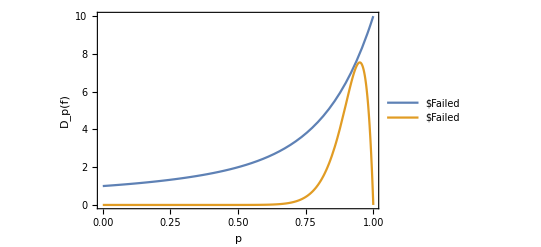

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all10.eps

```mathematica
<<MaTeX`
n = 10
DALL[p_,m_] = Sum[p^(i-1),{i,1,m}] 
LowerBound[p_,m_]=4*p(1-p)(m*p^(m-1))^2
LowerBound[p,n]
plot1 = Plot[{DALL[p,n], LowerBound[p,n]},{p,0,1},PlotLegends->{MaTeX@{"D_p(ALL_{10}^1)","4p(1-p)(\mathbf{I}^p(ALL_{10}^1))^2"}},Frame -> True,FrameLabel->{MaTeX@"p", MaTeX@"D_p(f)"},LabelStyle->{Black,Medium} ]
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all10.eps",plot1]
```